Define the geometric density with spending rate ψ and its inverse.  Note that it’s got an ugly inverse function.

```mathematica
Clear[g,K]
g[x_,ψ_]=K+Integrate[-ψ(1-ψ)^(x-1),x]
```

K-((1-ψ)^(-1+x) ψ)/Log[1-ψ]

```mathematica
Clear[h];
h[y_,ψ_]:= 1+(Log[-Log[1-ψ]]-Log[ψ]+Log[y-K])/Log[1-ψ]
```

```mathematica
FullSimplify[h[g[x,ψ],ψ],{x>0,ψ>0, ψ<1}]
```

x

```mathematica
FullSimplify[g[h[x,ψ],ψ],{x>0,ψ>0, ψ<1}]
```

x

For a simpler form, MM pushes terms into the log.

```mathematica
Clear[y,ψ]
FullSimplify[h[y,ψ],{x>0,ψ>0, ψ<1}]
```

Log[-((K-y) (-1+ψ) Log[1-ψ])/ψ]/Log[1-ψ]

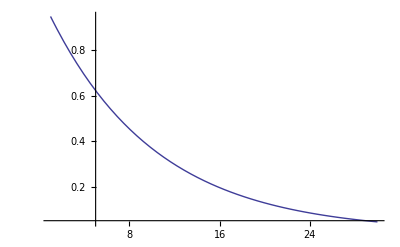

```mathematica
Plot[g[x,0.1],{x,1,30}, PlotRange->All]
```